# Configurações de Linhas de Transmissão

## Circuito Recapacitado 500kV

```mathematica
xy2={{-7.229, 8.639}, {-7.229, 10.500}, {-6.771, 10.500},
 {-6.771, 8.639}, {-0.229, 10.500},{-0.229, 9.876},
 {0.229, 9.876}, {0.229, 10.500}, {7.229, 8.639}, 
{7.229, 10.500}, {6.771, 10.500},{6.771, 8.639}, 
{-5.000, 20.500}, {5.000, 20.500}};
```

```mathematica
mostra2={Circle[#,.25]}&/@xy2;
```

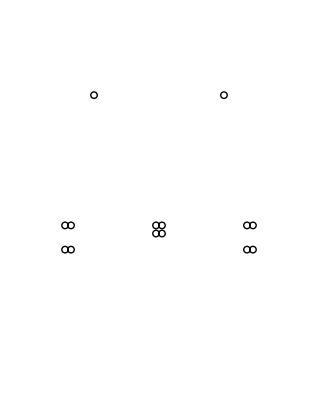

```mathematica
t2=Show[Graphics[mostra2],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-10,10},{-0.1,25}},FrameLabel->{"distância (m)","distância (m)"}]
```

## Circuito Convencional 500kV

```mathematica
xy3={{-11.000,10.736},{-10.771,11.132},{-11.229,11.132},
{0.000,10.736},{0.229,11.132},{-0.229,11.132},
{11.000,10.736},{10.771,11.132},{11.229,11.132},
{-6.000,22.000},{6.000,22.000}};
```

```mathematica
mostra3={Circle[#,.25]}&/@xy3;
```

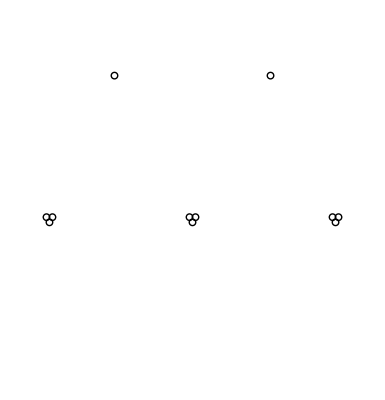

```mathematica
t3=Show[Graphics[mostra3],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-12.1,12.1},{-0.1,25}},FrameLabel->{"distância (m)","distância (m)"}]
```

## Circuito Compacto 500kV

```mathematica
xy4= {{-4.271, 10.771}, {-4.271, 11.229}, {-4.729, 11.229},
 {-4.729, 10.771}, {0.229, 15.271},{0.229, 15.729},
 {-0.229, 15.729}, {-0.229, 15.271}, {4.271, 10.771},
 {4.271, 11.229},{4.729, 11.229},{4.729, 10.771},
 {-3.500, 26.000}, {3.500, 26.000}};
```

```mathematica
mostra4={Circle[#,.25]}&/@xy4;
```

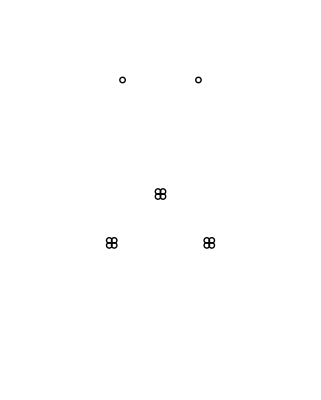

```mathematica
t4=Show[Graphics[mostra4],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-12.1,12.1},{-0.1,30}},FrameLabel->{"distância (m)","distância (m)"}]
```

## Linha em delta com feixes circulares simétricos 500kV

```mathematica
xy5={{-5.754,9.543},{-4.496,10.314},{-4.977,11.562},
{-6.529,11.562},{-7.009,10.314},{0.000,13.845},
{0.866,14.409},{0.535,15.317},{-0.535,15.317},
{-0.866,14.409},{5.754,9.543},{4.496,10.314},
{4.977,11.562},{6.529,11.562},{7.009,10.314},
{-4.000,23.961},{4.000,23.961}};
```

```mathematica
mostra5={Circle[#,.25]}&/@xy5;
```

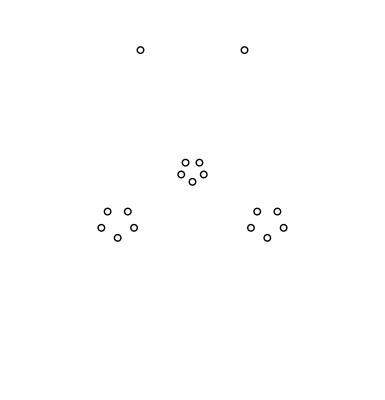

```mathematica
t5=Show[Graphics[mostra5],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-12.1,12.1},{-0.1,25}},FrameLabel->{"distância (m)","distância (m)"}]
```

## Linha com feixes elipticos simétricos 500kV

```mathematica
xy6={{-6.722,9.543},{-5.739,10.918},{-6.115,13.139},
{-7.330,13.139},{-7.706,10.918},{0.000,10.622},
{0.750,11.250},{0.465,12.267},{-0.465,12.267},
{-0.750,11.250},{6.722,9.543},{5.739,10.918},
{6.115,13.139},{7.330,13.139},{7.706,10.918},
{5.000,23.941},{-5.000,23.941}};
```

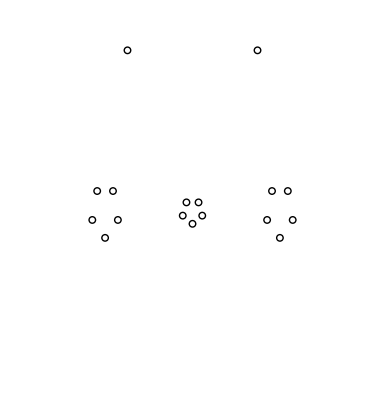

```mathematica
mostra6=({Circle[#1,0.25]}&)/@xy6;
t6=Show[Graphics[mostra6],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-12.1,12.1},{-0.1,25}},FrameLabel->{"distância (m)","distância (m)"}]
```

## Linha com distribuição horizontal genérica 500kV

```mathematica
xy7={{-6.000,9.000},{-5.253,9.000},{-5.642,10.400},
{-5.628,11.752},{-5.275,13.000},{-6.000,13.000},
{-0.342,9.942},{-0.681,11.025},{-0.342,12.108},
{0.342,12.108},{0.681,11.025},{0.342,9.942},
{6.000,9.000},{5.253,9.000},{5.642,10.400},
{5.628,11.752},{5.275,13.000},{6.000,13.000},
{-4.000,23.000},{4.000,23.000}};
```

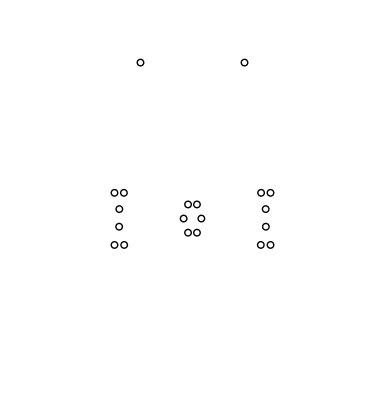

```mathematica
mostra7=({Circle[#1,0.25]}&)/@xy7;
t7=Show[Graphics[mostra7],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-12.1,12.1},{-0.1,25}},FrameLabel->{"distância (m)","distância (m)"}]
```

## Linha com distribuição vertical de forma genérica 500kV

```mathematica
xy8={{0.000,10.000},{-2.165,10.122},{-4.000,10.566},
{-4.000,10.000},{4.000,10.000},{4.000,10.566},
{2.165,10.122},{0.000,16.315},{-1.691,16.103},
{-2.751,16.754},{-2.852,16.455},{2.852,16.455},
{2.751,16.754},{1.691,16.103},{0.000,23.500},
{-1.399,22.599},{-3.500,22.707},{-3.500,23.500},
{3.500,23.500},{3.500,22.707},{1.399,22.599},
{-5.000,33.500},{5.000,33.500}};
```

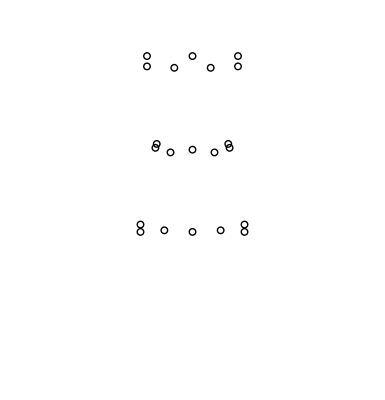

```mathematica
mostra8=({Circle[#1,0.25]}&)/@xy8;
t8=Show[Graphics[mostra8],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-12.1,12.1},{-0.1,25}},FrameLabel->{"distância (m)","distância (m)"}]
```